```mathematica
Remove["Global`*"]
```

# ComplexMatrixDraw

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells with possibly
	- a frame and a central point
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	offset : a list {Δx,Δy} (default is {0,0}) indicating how to shift the cell in the xy plane
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position ij returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderColor: Color of the 2D shape border (default is Black).
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π . 
		- thicknessShape: thickness of the shape border (default is 0.01, i.e 1% of the cell).
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- thicknessArrow: thickness of the arrow border (default is 0.01, i.e 1% of the whole graph).
		- arrowColor: Color of the arow (default is Black).
		- arrowSize: Size of the arrow in fraction of the whole graph  (default is 0.05, i.e. 5%).
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{offset -> {0,0}, 
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderColor->Black,fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),thicknessShape->.001,
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,thicknessArrow->.001,arrowSize->.05,arrowColor->Black,
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=(position-0.5{1,1})+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[{Thickness[OptionValue[thicknessShape]],OptionValue[borderColor]}],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow={OptionValue[arrowColor],Thickness[OptionValue[thicknessArrow]],Arrowheads[OptionValue[arrowSize]],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]}];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
Graphics[frame~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
ComplexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
ComplexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
ComplexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,(Reverse[#2]){1,-1},opts]&,matrix,{2}]];
ComplexMatrixDrawInverse[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,(Reverse[{#2[[1]],#2[[1]]+#2[[2]]-1 }] ){1,-1},opts]&,matrix,{2}]];
ComplexMatrixDrawLower[matrix_,opts___]:=Block[{tt=MapIndexed[Take[#1,#2[[1]]]&,matrix,1]},ComplexMatrixDraw[tt,opts]];
ComplexMatrixDrawUpper[matrix_,opts___]:=Block[{tt=MapIndexed[Take[#1,-(Max[Map[Dimensions[#1][[1]]&,matrix]]+1-#2[[1]])]&,matrix,1]},ComplexMatrixDrawInverse[tt,opts]];
ComplexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,(Reverse[#2]){1,-1},opts]&,matrix,{2}]];
```

### Examples

Works on numbers, vectors, and arrays, even with null elements,

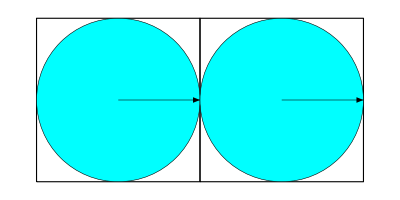
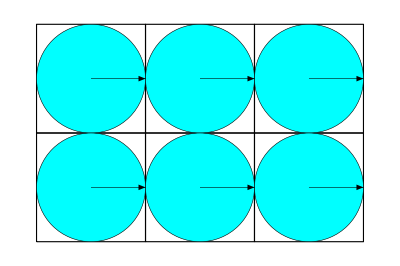
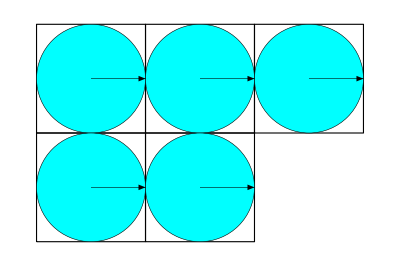
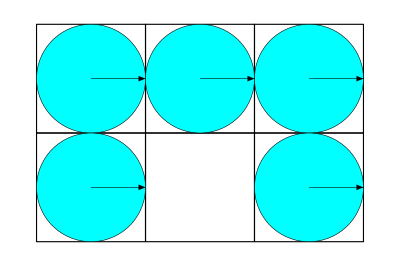
{complexMatrixDraw[{{1}}],complexMatrixDraw[{{1},{1}}],-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComplexMatrixDraw/@ {1,{1,1},{{1,1}},{{1,1,1},{1,1,1}},{{1,1,1},{1,1}},{{1,1,1},{1,,1}}}
```

Default color scheme

```mathematica
Animate[ComplexMatrixDraw[abs Exp[I φ]],{{abs,0.5},0,1},{φ,0,2π},AnimationRunning->False]
```

Single cell with the  default options and other options

```mathematica
default={};options[1]=default;
options[2]={show2DShape->False};
options[3]={showArrow->False};
options[4]={whatShape->"square"};
options[5]={functionFor2DShapeAera->(Abs[#]^2&)};
options[6]={hideArrowSmallerThan->0.1};
options[7]={fill2DShape->False};
options[8]={frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]] &)};
options[9]={showCentralPoint->True};
options[10]={showLabel->True,labelFunction->((ToString[Round[1000Abs[#]]/10.]<>"%")&), labelStyle->Medium,labelShift->{0,0.3},fill2DShape->False};
options[11]= {offset -> {1,2}};
optionSets=Table[options[i],{i,11}];
```

```mathematica
c=0.499(1+I)/Sqrt[2];
ComplexMatrixDraw[c,Sequence@@#]&/@optionSets
```

{complexMatrixDraw[{{0.352846+0.352846 ⅈ}}],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},show2DShape→False],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},showArrow→False],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},whatShape→square],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},functionFor2DShapeAera→(Abs[#1]^2&)],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},hideArrowSmallerThan→0.1],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},fill2DShape→False],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},frameFaceFunction→(GrayLevel[1-0.2 KroneckerDelta[#1,-#2]]&)],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},showCentralPoint→True],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},showLabel→True,labelFunction→(ToString[Round[1000 Abs[#1]]/10.]<>%&),labelStyle→Medium,labelShift→{0,0.3},fill2DShape→False],complexMatrixDraw[{{0.352846+0.352846 ⅈ}},offset→{1,2}]}

Rectangular matrix with the  default options and different options

(1 | 1 | 1
ⅇ^((ⅈ π)/4) | 1/2 | 1/2 ⅇ^((ⅈ π)/4)
ⅈ | 1/4 | ⅈ/4
ⅇ^((3 ⅈ π)/4) | 1/20 | 1/20 ⅇ^((3 ⅈ π)/4))

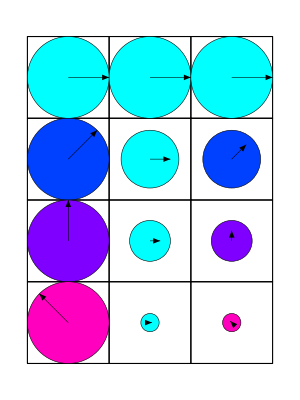
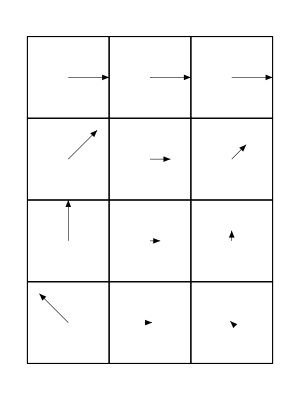
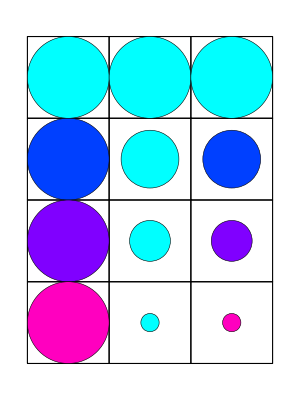
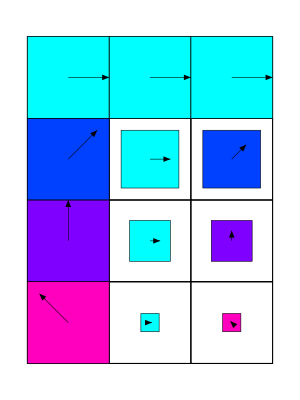
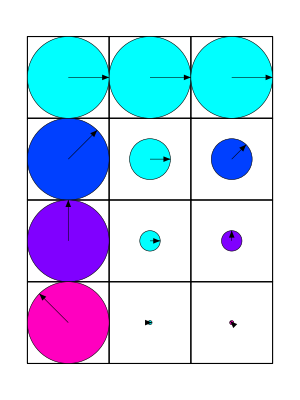
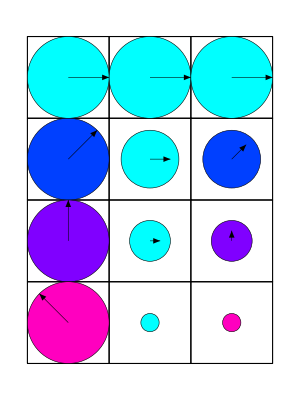
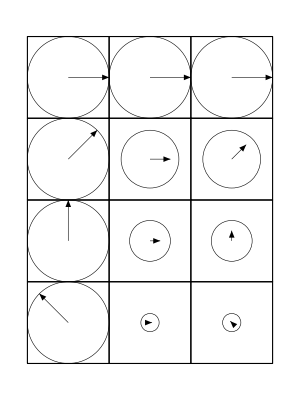
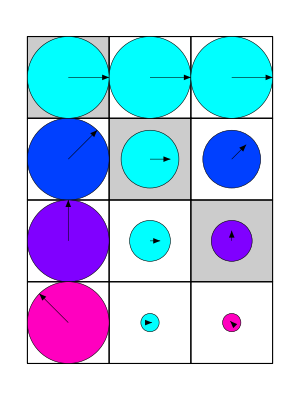
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(matrix1={{1,Exp[I π/4],Exp[I π/2],Exp[I 3π/4]},{1,1/2,1/4,1/20},{1,1/2 Exp[I π/4],1/4  Exp[I π/2],1/20Exp[I 3 π/4]}}//Transpose)//MatrixForm
ComplexMatrixDraw[matrix1,Sequence@@#]&/@optionSets
```

Comparison of two matrices

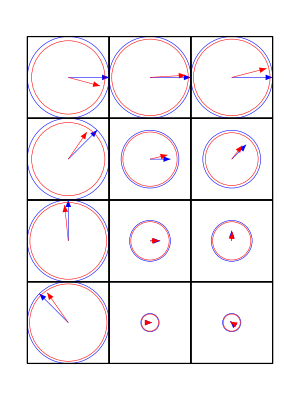
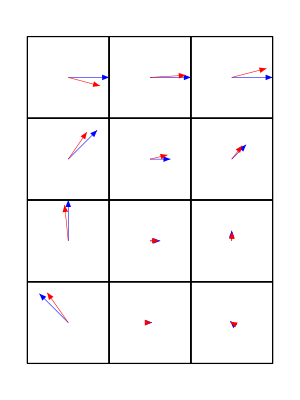
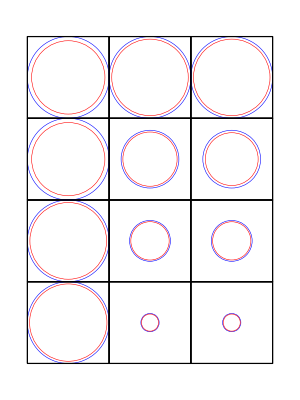
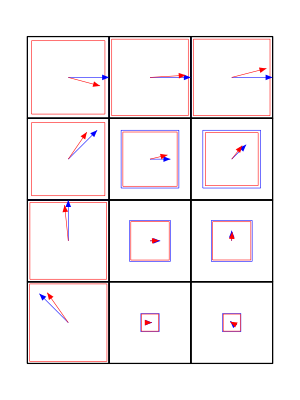
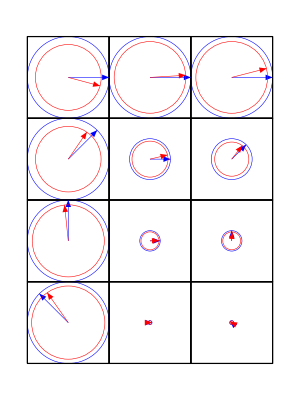
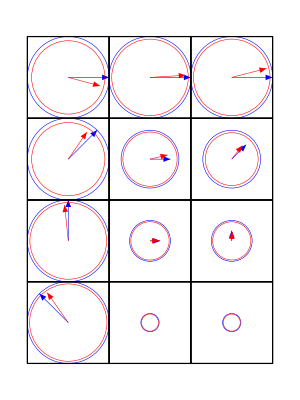
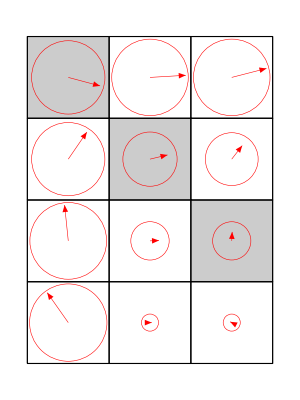
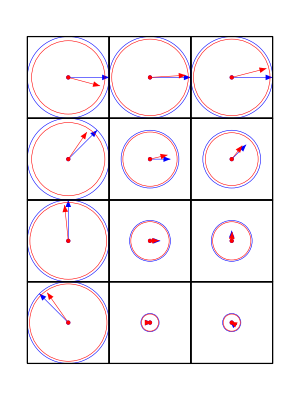
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gr1=ComplexMatrixDraw[matrix1,Sequence@@#]&/@(Join[{borderColor->Blue,arrowColor->Blue,fill2DShape->False},#]&/@optionSets);(matrix2=Map[(1-RandomReal[{0.1,0.2}])Exp[I RandomReal[{-π/10.,π/10}]]#&, matrix1,{2}])//MatrixForm;
gr2=ComplexMatrixDraw[matrix2,Sequence@@#]&/@(Join[{borderColor->Red,thicknessShape->.001,arrowColor->Red,thicknessArrow->0.001,fill2DShape->False,labelShift->{0,-0.3}},#]&/@optionSets);
MapThread[Show[{#1,#2}]&,{gr1,gr2}]
```

```mathematica
process = {{1,0,0,0},{0,1./Sqrt[2],1./Sqrt[2],0},{0,1./Sqrt[2],1./Sqrt[2],0},{0,0,0,1}}
```

{{1,0,0,0},{0,0.707107,0.707107,0},{0,0.707107,0.707107,0},{0,0,0,1}}

```mathematica
dir := "L:/local-expdata/FO-C5/3rd-Run/2011_04_21/matrices - quantum process tomography at 31 ns - 16/"
chireal:= Import[dir <> "chi_real_real.txt","Table"];
chiimag :=Import[dir <> "chi_real_imag.txt","Table"];
chifitreal:= Import[dir <> "chi_best_fit_real.txt","Table"];
chifitimag :=Import[dir <> "chi_best_fit_imag.txt","Table"];
chiidreal :=Import[dir <> "chi_ideal_real.txt","Table"];
chiidimag :=Import[dir <> "chi_ideal_imag.txt","Table"];
chi :=chireal+I*chiimag
chifit :=chifitreal+I*chifitimag
chiid :=chiidreal+I*chiidimag
```

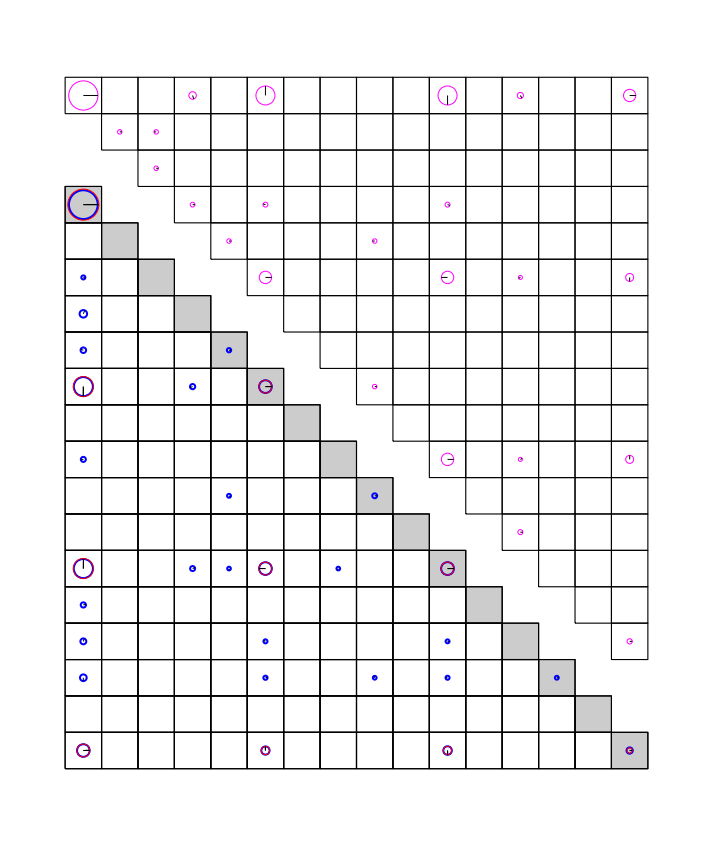

```mathematica
opts := {showCentralPoint -> False,functionFor2DShapeAera->If[Abs[#] > 0.01, (Abs[#]&),0],fill2DShape -> False,arrowSize -> 0.0,hideArrowSmallerThan -> 0.02,functionForArrowLength -> If[Abs[#] > 0.01,(Sqrt[Abs[#]]&),0]}
Show[ComplexMatrixDrawUpper [chifit,opts,thicknessShape -> 0.001,borderColor ->Magenta,frameFaceFunction->({White,Opacity[0]}&),offset ->{0,3}],ComplexMatrixDrawLower [chi,thicknessShape -> 0.002,frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]] &),opts,borderColor -> Blue,offset ->{0,0}],ComplexMatrixDrawLower [chiid,thicknessShape -> 0.001,borderColor -> Red,opts,frameFaceFunction->({White,Opacity[0]}&),offset ->{0,0}]]
```

## Calculate the Kraus operators of the process

```mathematica
idreal :=Import[dir <> "chi_ideal_real.txt","Table"];
dir := "L:/local-expdata/FO-C5/3rd-Run/2011_04_21/matrices - quantum process tomography at 31 ns - 16/kraus operators/";
ops = Map[ (Import[dir <> "a_"<>ToString[#1]<>"_real.txt","Table"]+I*Import[dir <> "a_"<>ToString[#1]<>"_imag.txt","Table"])&,Range[1,16]];
```

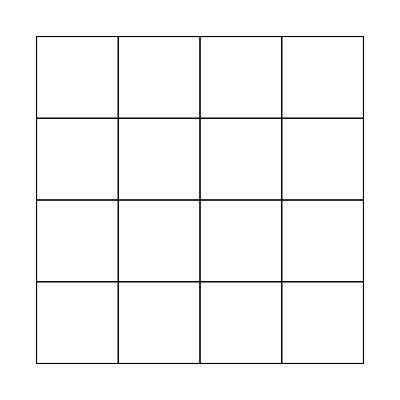
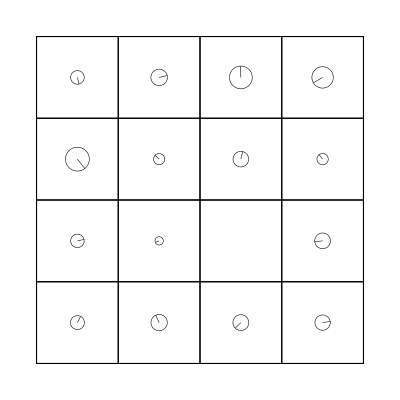
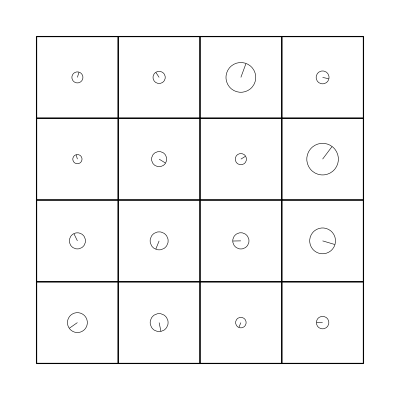
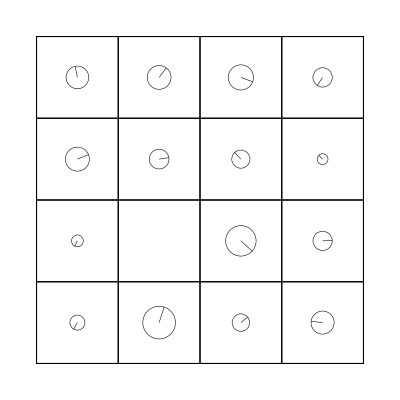
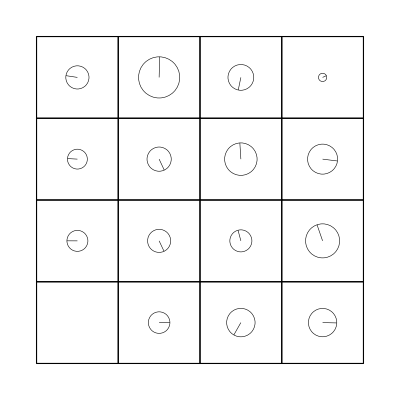
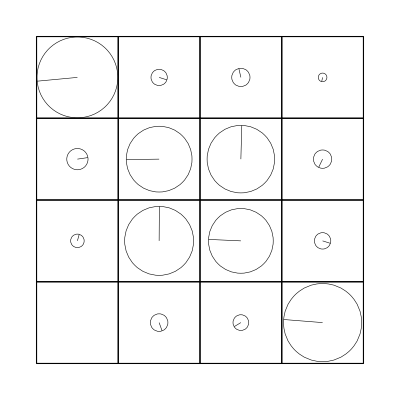

```mathematica
opts := {showCentralPoint -> False,functionFor2DShapeAera->If[Abs[#] > 0.01, (Abs[#]&),0],fill2DShape -> False,arrowSize -> 0.0,hideArrowSmallerThan -> 0.02,functionForArrowLength -> If[Abs[#] > 0.01,(Sqrt[Abs[#]]&),0]}
Map[ComplexMatrixDraw[ops[[#1]],opts]&,Range[-6,-1]]
```

```mathematica
eigenvals = Import[dir <> "eigenvalues.txt","Table"]
```

{{-4.253764608956493×10^-13},{-1.3276408007190886×10^-14},{-3.5336728385772392×10^-15},{-1.3544057758472266×10^-15},{2.9574362781909815×10^-15},{3.9007492693637516×10^-15},{7.9196443732030658×10^-15},{1.4368170597322317×10^-14},{2.6328929916241715×10^-14},{6.6987870652547311×10^-14},{5.9418069974954482×10^-13},{0.0074736771669643631},{0.016176409873585786},{0.024140843124831241},{0.053694739415636315},{0.89851433041890949}}

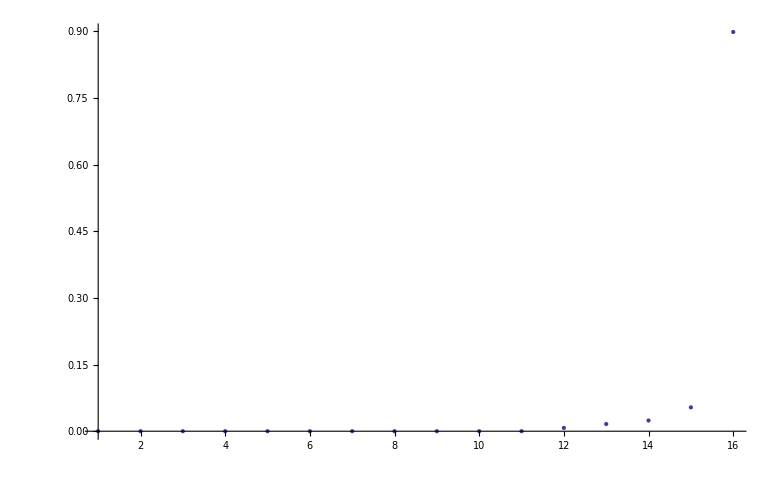

```mathematica
ListPlot[MapIndexed[{#2[[1]],#1}&,Flatten[eigenvals]],PlotRange -> All]
```